## Determinants and weird points

Here, we import the data files with the determinants of the classical Fisher information (CFI) matrices for each value of N (number of probes) for all values of (Bx, Bz) in the square region Bx ϵ [0,π], Bz ϵ [0,π].  
The (Bx, Bz) points for which the determinant of the CFI matrix is a finite value increases monotonically with N are classified as “normal points”.  The values for which this is not the case  (either because they have infinite values, indeterminate values, or the sequence does not increase monotonically with N) are classified as “weird points”.  
The (Bx, Bz) points classified as “weird” do not result in inverse CFI matrices with elements that decrease with increasing N; hence the label “weird” (although this might not be the most descriptive name).

Det::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Det::mindet will be suppressed during this calculation.

Det::inf: Input matrix contains an infinite entry.

General::stop: Further output of Det::inf will be suppressed during this calculation.

Import::nffil: File C:\Users\ruiyangzhou\Desktop\Mauricio\Results\Bx0.75Bz0.75\noQECGHZZdet.mx not found during Import.

Import::nffil: File C:\Users\ruiyangzhou\Desktop\Mauricio\Results\Bx0.75Bz0.75\noQECGHZXdet.mx not found during Import.

Import::nffil: File C:\Users\ruiyangzhou\Desktop\Mauricio\Results\Bx0.75Bz0.75\noQEC2GHZdet.mx not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

OrderedQ::normal: Nonatomic expression expected at position 1 in OrderedQ[$Failed].

General::stop: Further output of OrderedQ::normal will be suppressed during this calculation.

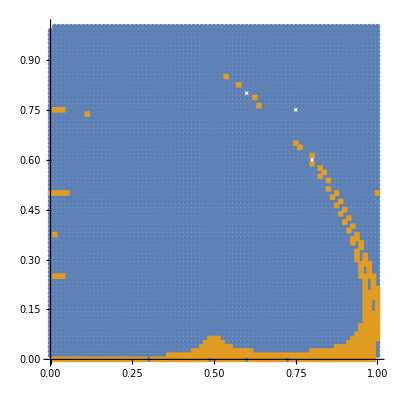

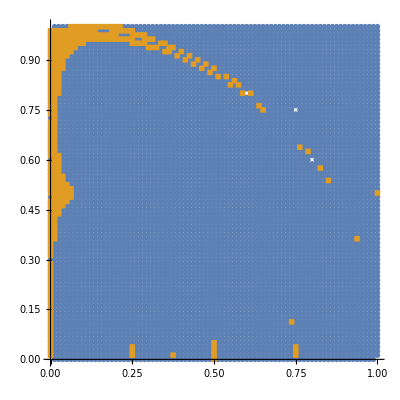

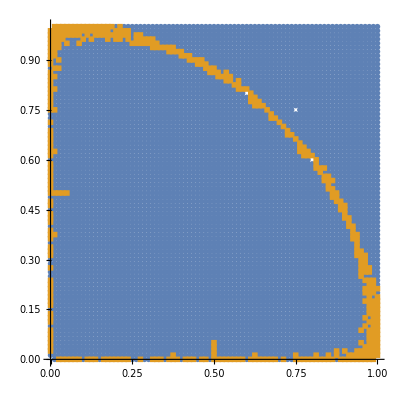

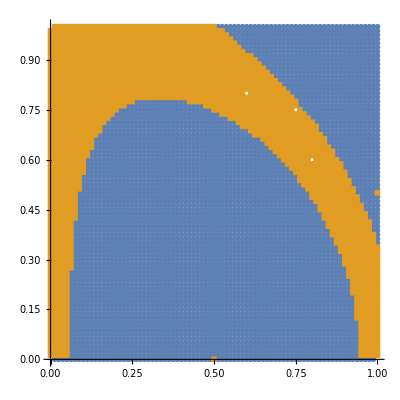

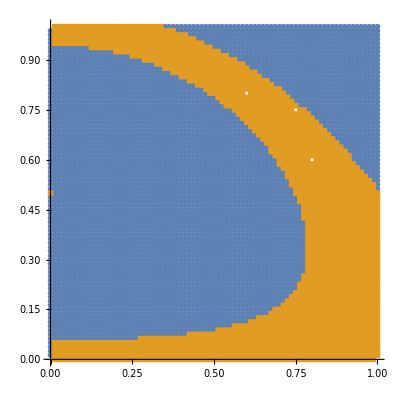

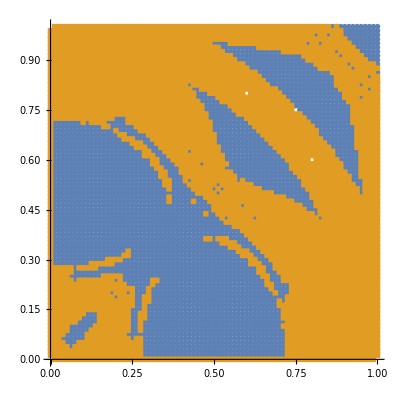

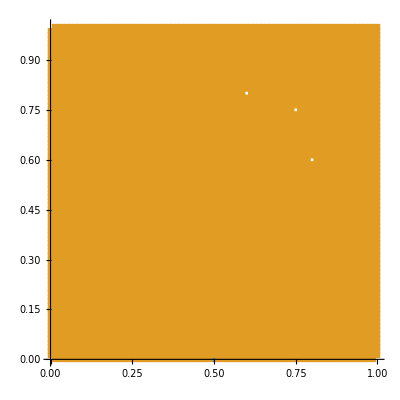

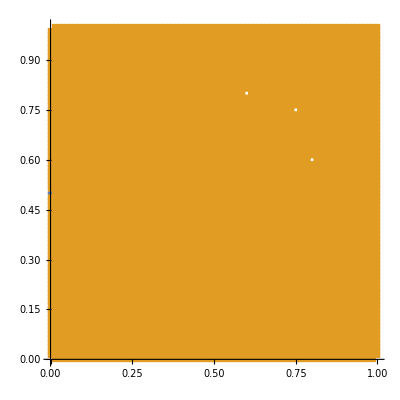

```mathematica
nmin=3;
nmax=101;
minB=0.0;
maxB=1.0;
stepB=0.0125;
(* ndet=3;
nindex=(ndet-1)/2; *)

(* Lists labeled by the kind of protocol and GHZ state(s) used *)

(* Z: GHZ state in the Z basis = |0...0> + |1...1> *)
(* X: GHZ state in the X basis = |+...+> + |-...-> *)
(* 2: both GHZ states *)

(* no: no QEC *)
WeirdPointsnoZ={};
NormalPointsnoZ={};
WeirdPointsnoX={};
NormalPointsnoX={};
WeirdPointsno2={};
NormalPointsno2={};

(* n: QEC with the magnetic field B acting on all N qubits *)
WeirdPointsnZ={};
NormalPointsnZ={};
WeirdPointsnX={};
NormalPointsnX={};
WeirdPointsn2={};
NormalPointsn2={};

(* n1: QEC with the magnetic field acting on all but the first qubit *)
WeirdPointsn1Z={};
NormalPointsn1Z={};
WeirdPointsn1X={};
NormalPointsn1X={};
WeirdPointsn12={};
NormalPointsn12={};

WeirdPoints={{},{},{},{},{},{},{},{},{}};
NormalPoints={{},{},{},{},{},{},{},{},{}};


(* Main loop *)
For[Bxaux=minB,Bxaux<=maxB,Bxaux+=stepB,
For[Bzaux=minB,Bzaux<=maxB,Bzaux+=stepB,

(* Print["(Bx, Bz) = (", Bxaux, ", ", Bzaux, ")" ]; *)

(* If the magnitude of the field is 0 or Pi, we end up in the same initial state *)
Bauxsq=Bxaux^2+Bzaux^2;
If[(Bauxsq==0)||(Bauxsq==1),Continue[]];

(* Folder path (be sure to change this path depending on where you saved the data files) *)
folderName=StringJoin["Bx",ToString[Bxaux],"Bz",ToString[Bzaux]];
folderPath=FileNameJoin[{"C:","Users","ruiyangzhou","Desktop","Mauricio","Results",folderName}];

(* Import the files with the determinants *)
noZ=Import[FileNameJoin[{folderPath,"noQECGHZZdet.mx"}]];
noX=Import[FileNameJoin[{folderPath,"noQECGHZXdet.mx"}]];
no2=Import[FileNameJoin[{folderPath,"noQEC2GHZdet.mx"}]];
nZ=Import[FileNameJoin[{folderPath,"nQECGHZZdet.mx"}]];
nX=Import[FileNameJoin[{folderPath,"nQECGHZXdet.mx"}]];
n2=Import[FileNameJoin[{folderPath,"nQEC2GHZdet.mx"}]];
n1Z=Import[FileNameJoin[{folderPath,"n1QECGHZZdet.mx"}]];
n1X=Import[FileNameJoin[{folderPath,"n1QECGHZXdet.mx"}]];
n12=Import[FileNameJoin[{folderPath,"n1QEC2GHZdet.mx"}]];

alldetlist={noZ,noX,no2,nZ,nX,n2,n1Z,n1X,n12};

(* AppendTo[noQECGHZZdetlist,{Bxaux,Bzaux,noQECGHZZdet[[nindex]]}];
AppendTo[noQECGHZXdetlist,{Bxaux,Bzaux,noQECGHZXdet[[nindex]]}];
AppendTo[noQEC2GHZdetlist,{Bxaux,Bzaux,noQEC2GHZdet[[nindex]]}];
AppendTo[nQECGHZZdetlist,{Bxaux,Bzaux,nQECGHZZdet[[nindex]]}];
AppendTo[nQECGHZXdetlist,{Bxaux,Bzaux,nQECGHZXdet[[nindex]]}];
AppendTo[nQEC2GHZdetlist,{Bxaux,Bzaux,nQEC2GHZdet[[nindex]]}];
AppendTo[n1QECGHZZdetlist,{Bxaux,Bzaux,n1QECGHZZdet[[nindex]]}];
AppendTo[n1QECGHZXdetlist,{Bxaux,Bzaux,n1QECGHZXdet[[nindex]]}];
AppendTo[n1QEC2GHZdetlist,{Bxaux,Bzaux,n1QEC2GHZdet[[nindex]]}]; *)

For[i=1,i<=9,i++,

(* The (Bx,Bz) point is classified as weird if either one of the two conditions are True *)

(* The list of determinants has an infinite or indeterminate element *)
cond1=MemberQ[alldetlist[[i]],ComplexInfinity]||MemberQ[alldetlist[[i]],Indeterminate];

(*  The numbers do not increase monotonically *)
cond2=!OrderedQ[alldetlist[[i]]];
If[cond1||cond2,
(
AppendTo[WeirdPoints[[i]],{Bxaux,Bzaux}];
),
(
AppendTo[NormalPoints[[i]],{Bxaux,Bzaux}];
)
];
];
];


];
folderPath=FileNameJoin[{"C:","Users","ruiyangzhou","Desktop","Mauricio","Results"}];
PlotA=ListPlot[{WeirdPoints[[1]],NormalPoints[[1]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsnoZ.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[2]],NormalPoints[[2]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsnoX.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[3]],NormalPoints[[3]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsno2.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[4]],NormalPoints[[4]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsnZ.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[5]],NormalPoints[[5]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsnX.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[6]],NormalPoints[[6]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsn2.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[7]],NormalPoints[[7]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsn1Z.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[8]],NormalPoints[[8]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsn1X.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[9]],NormalPoints[[9]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175}]
Export[FileNameJoin[{folderPath,"WeirdPointsn12.pdf"}],PlotA];
```

```mathematica
folderPath=FileNameJoin[{"C:","Users","ruiyangzhou","Desktop","Mauricio","Results"}];
Export[FileNameJoin[{folderPath,"WeirdPoints_NoQEC_Z.mx"}],WeirdPoints[[1]]];
Export[FileNameJoin[{folderPath,"NormalPoints_NoQEC_Z.mx"}],NormalPoints[[1]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_NoQEC_X.mx"}],WeirdPoints[[2]]];
Export[FileNameJoin[{folderPath,"NormalPoints_NoQEC_X.mx"}],NormalPoints[[2]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_NoQEC_2.mx"}],WeirdPoints[[3]]];
Export[FileNameJoin[{folderPath,"NormalPoints_NoQEC_2.mx"}],NormalPoints[[3]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_nQEC_Z.mx"}],WeirdPoints[[4]]];
Export[FileNameJoin[{folderPath,"NormalPoints_nQEC_Z.mx"}],NormalPoints[[4]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_nQEC_X.mx"}],WeirdPoints[[5]]];
Export[FileNameJoin[{folderPath,"NormalPoints_nQEC_X.mx"}],NormalPoints[[5]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_nQEC_2.mx"}],WeirdPoints[[6]]];
Export[FileNameJoin[{folderPath,"NormalPoints_nQEC_2.mx"}],NormalPoints[[6]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_n1QEC_Z.mx"}],WeirdPoints[[7]]];
Export[FileNameJoin[{folderPath,"NormalPoints_n1QEC_Z.mx"}],NormalPoints[[7]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_n1QEC_X.mx"}],WeirdPoints[[8]]];
Export[FileNameJoin[{folderPath,"NormalPoints_n1QEC_X.mx"}],NormalPoints[[8]]];
Export[FileNameJoin[{folderPath,"WeirdPoints_n1QEC_2.mx"}],WeirdPoints[[9]]];
Export[FileNameJoin[{folderPath,"NormalPoints_n1QEC_2.mx"}],NormalPoints[[9]]];
```

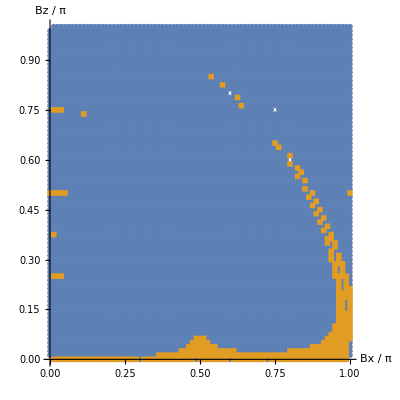

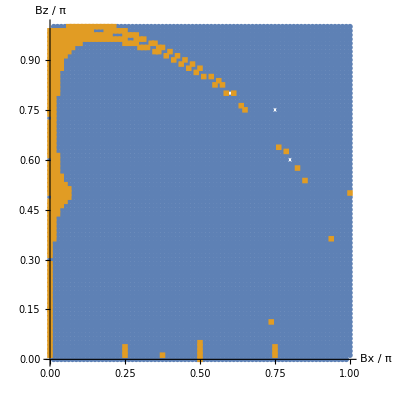

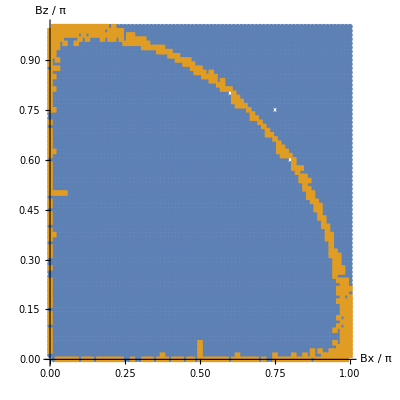

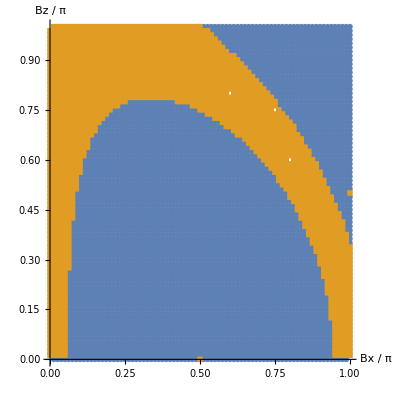

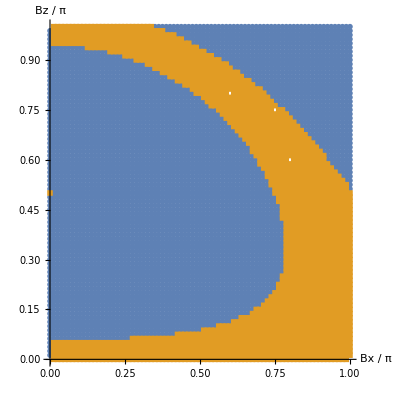

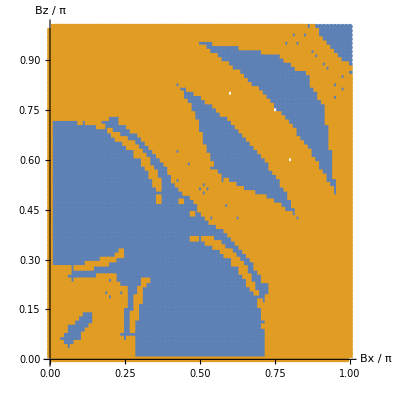

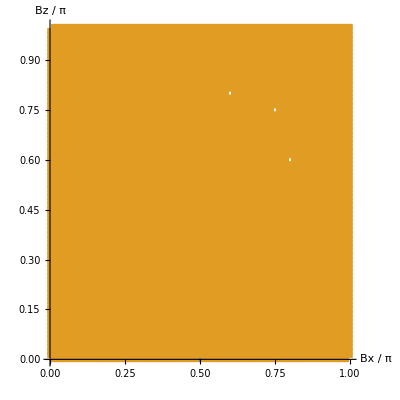

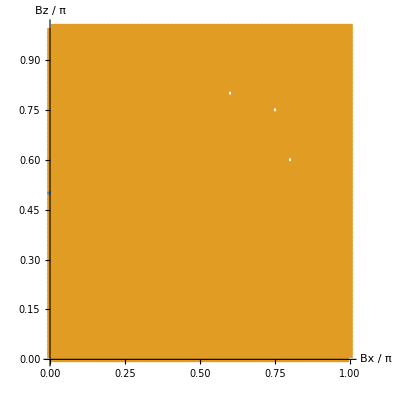

```mathematica
folderPath=FileNameJoin[{"C:","Users","ruiyangzhou","Desktop","Mauricio","Results"}];
PlotA=ListPlot[{WeirdPoints[[1]],NormalPoints[[1]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsnoZ.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[2]],NormalPoints[[2]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsnoX.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[3]],NormalPoints[[3]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsno2.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[4]],NormalPoints[[4]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsnZ.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[5]],NormalPoints[[5]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsnX.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[6]],NormalPoints[[6]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsn2.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[7]],NormalPoints[[7]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsn1Z.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[8]],NormalPoints[[8]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsn1X.pdf"}],PlotA];
PlotA=ListPlot[{WeirdPoints[[9]],NormalPoints[[9]]},AspectRatio->1,PlotMarkers->{Automatic,0.0175},AxesLabel->{"Bx / π","Bz / π"}]
Export[FileNameJoin[{folderPath,"WeirdPointsn12.pdf"}],PlotA];
```

## Scratch paper

The rest of the file is essentially scratch paper.  Feel free to ignore everything from here on.

```mathematica
(*Specify the folder path*)
folderName=StringJoin["Bx",ToString[0.5],"Bz",ToString[0]];
folderPath=FileNameJoin[{"C:","Users","ruiyangzhou","Desktop","Mauricio","Results",folderName}];
noQECGHZZdet=Import[FileNameJoin[{folderPath,"noQECGHZZdet.mx"}]]
OrderedQ[noQECGHZZdet]
nQECGHZZdet=Import[FileNameJoin[{folderPath,"nQECGHZZdet.mx"}]]
OrderedQ[nQECGHZZdet]
n1QECGHZZdet=Import[FileNameJoin[{folderPath,"n1QECGHZZdet.mx"}]]
OrderedQ[n1QECGHZZdet]
noQECGHZXdet=Import[FileNameJoin[{folderPath,"noQECGHZXdet.mx"}]]
OrderedQ[noQECGHZXdet]
nQECGHZXdet=Import[FileNameJoin[{folderPath,"nQECGHZXdet.mx"}]]
OrderedQ[nQECGHZXdet]
n1QECGHZXdet=Import[FileNameJoin[{folderPath,"n1QECGHZXdet.mx"}]]
OrderedQ[n1QECGHZXdet]
noQEC2GHZdet=Import[FileNameJoin[{folderPath,"noQEC2GHZdet.mx"}]]
OrderedQ[noQEC2GHZdet]
nQEC2GHZdet=Import[FileNameJoin[{folderPath,"nQEC2GHZdet.mx"}]]
OrderedQ[nQEC2GHZdet]
n1QEC2GHZdet=Import[FileNameJoin[{folderPath,"n1QEC2GHZdet.mx"}]]
OrderedQ[n1QEC2GHZdet]
```

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

True

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

{51.8764,415.012,1400.66,3320.09,6484.56,11205.3,17793.6,26560.7,37817.9,51876.4,69047.5,89642.5,113973.,142349.,175083.,212486.,254869.,302543.,355821.,415012.,480428.,552380.,631181.,717140.,810569.,911780.,1.02108×10^6,1.13879×10^6,1.26521×10^6,1.40066×10^6,1.54545×10^6,1.69989×10^6,1.86428×10^6,2.03895×10^6,2.2242×10^6,2.42035×10^6,2.6277×10^6,2.84656×10^6,3.07726×10^6,3.32009×10^6,3.57538×10^6,3.84342×10^6,4.12454×10^6,4.41904×10^6,4.72724×10^6,5.04945×10^6,5.38597×10^6,5.73712×10^6,6.10321×10^6,6.48456×10^6}

True

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

Det::mindet: Input matrix contains an indeterminate entry.

{Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}],Det[{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}]}

True

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

True

```mathematica
OrderedQ[{1,2,3}]
OrderedQ[{1,2,2,3}]
OrderedQ[{3,2,1}]
```

True

True

False

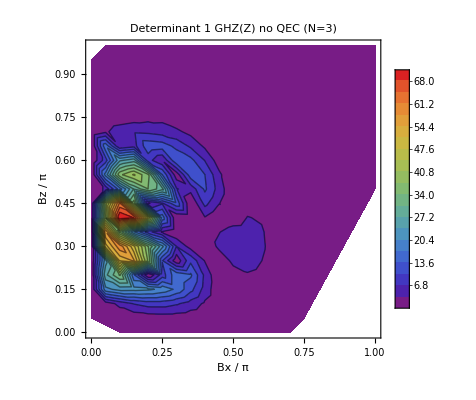

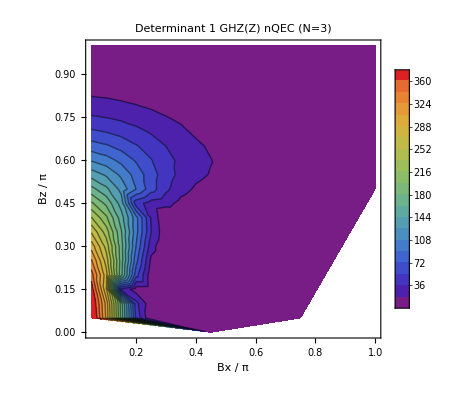

```mathematica
PlotA=ListContourPlot[noQECGHZZdetlist,InterpolationOrder->2,FrameLabel->{"Bx / π","Bz / π"},ColorFunction->"Rainbow",Contours->20,PlotLabel->"Determinant 1 GHZ(Z) no QEC (N=3)",PlotRange->All,PlotLegends->Automatic]
PlotA=ListContourPlot[nQECGHZZdetlist,InterpolationOrder->2,FrameLabel->{"Bx / π","Bz / π"},ColorFunction->"Rainbow",Contours->20,PlotLabel->"Determinant 1 GHZ(Z) nQEC (N=3)",PlotRange->All,PlotLegends->Automatic]
```